```mathematica
<<FormsAndVectors`
SetOptions[Simplify,Trig->False]
```

{Assumptions:>$Assumptions,ComplexityFunction→Automatic,ExcludedForms→{},TimeConstraint→300,TransformationFunctions→Automatic,Trig→False}

```mathematica
$Assumptions=0<u&&u<π&&0≤v&&v<2π&&t>0&&v>0&&v<2π&&Det[g]>0&&Cos[v]^2+Sin[v]^2==1&&Cos[u]^2+Sin[u]^2==1(*&&a>0*)&&b>0&&c>0;
XG={x[u,v],y[u,v],z[u,v]};
XS={Sin[u]Cos[v],Sin[u]Sin[v],Cos[u]}; 
XQ=XS+Cos[u]*{1,0,0};
XPolXY={v*Cos[u],v*Sin[u],0};
XGXY={x[u,v],y[u,v],0};
cx=1
cy=1
cz=b
XE={cx*Sin[u] Cos[v],cy*Sin[u] Sin[v],cz*Cos[u]}
X= XE
g=MetricFromPara[X,u,v]//Simplify
gInv=Inverse[g]//Simplify
vol= Sqrt[Det[g]]//Simplify
repRulesS={Cot[u]->z/Sqrt[1-z^2],Cos[u]->z,Sin[u]->Sqrt[1-z^2],Sin[v]->y/Sqrt[1-z^2],Cos[v]->x/Sqrt[1-z^2],Cos[u/2]->Sqrt[(1+z)/2],Sec[u/2]->Sqrt[2/(1+z)],Csc[u]->1/Sqrt[1-z^2]};
repRulesE={Cos[u]->z/cz,Sin[u]->Sqrt[1-Cos[u]^2],Cos[v]->x/(cx*Sin[u]),Sin[v]->y/(cy*Sin[u]),Sin[2*u]->2*Sin[u]*Cos[u],Csc[u]->1/Sqrt[1-Cos[u]^2]};
ySubS={y->Sqrt[1-x^2-z^2]};
zSubS={z->Sqrt[1-x^2-y^2]};
zSubE={z->cz*Sqrt[1-y^2/cy^2-x^2/cx^2]};
ySubE={y->cy*Sqrt[1-z^2/cz^2-x^2/cx^2]};
repRules=repRulesS
zSub = zSubS
```

1

1

b

{Cos[v] Sin[u],Sin[u] Sin[v],b Cos[u]}

{Cos[v] Sin[u],Sin[u] Sin[v],b Cos[u]}

{{1+(-1+b^2) Sin[u]^2,0},{0,Sin[u]^2}}

{{1/(1+(-1+b^2) Sin[u]^2),0},{0,Csc[u]^2}}

√(Sin[u]^2+(-1+b^2) Sin[u]^4)

{Cot[u]→z/(√(1-z^2)),Cos[u]→z,Sin[u]→√(1-z^2),Sin[v]→y/(√(1-z^2)),Cos[v]→x/(√(1-z^2)),Cos[u/2]→(√(1+z))/(√2),Sec[u/2]→√2 √(1/(1+z)),Csc[u]→1/(√(1-z^2))}

{z→√(1-x^2-y^2)}

```mathematica
Xu=D[X,u]//Simplify
Xv=D[X,v]//Simplify
nuDirection=Cross[Xu,Xv]//Simplify;
nu=(1/Sqrt[nuDirection.nuDirection])*nuDirection//Simplify
```

{Cos[u] Cos[v],Cos[u] Sin[v],-b Sin[u]}

{-Sin[u] Sin[v],Cos[v] Sin[u],0}

{(b Cos[v] Sin[u])/(√(1+(-1+b^2) Sin[u]^2)),(b Sin[u] Sin[v])/(√(1+(-1+b^2) Sin[u]^2)),Cos[u]/(√(1+(-1+b^2) Sin[u]^2))}

```mathematica
HVec=Table[LBeltrami0[X[[i]],u,v,g],{i,3}]//Simplify;
H=HVec.nu//Simplify
```

-(b (b^2+Cot[u]^2+Csc[u]^2))/((-1+b^2+Csc[u]^2) √(1+(-1+b^2) Sin[u]^2))

```mathematica
Xuu=D[Xu,u]//Simplify;
Xuv=D[Xu,v]//Simplify;
Xvv=D[Xv,v]//Simplify;
II={{nu.Xuu,nu.Xuv},{nu.Xuv,nu.Xvv}}//Simplify
S=Inverse[g].II//Simplify
B=II.Inverse[g]//Simplify
Tr[S]//Simplify
Tr[S]-H//Simplify
K=Det[S]//Simplify
```

{{-b/(√(1+(-1+b^2) Sin[u]^2)),0},{0,-(b Sin[u]^2)/(√(1+(-1+b^2) Sin[u]^2))}}

{{-b/((1+(-1+b^2) Sin[u]^2)^(3/2)),0},{0,-b/(√(1+(-1+b^2) Sin[u]^2))}}

{{-b/((1+(-1+b^2) Sin[u]^2)^(3/2)),0},{0,-b/(√(1+(-1+b^2) Sin[u]^2))}}

(-2 b+(b-b^3) Sin[u]^2)/((1+(-1+b^2) Sin[u]^2)^(3/2))

0

b^2/((1+(-1+b^2) Sin[u]^2)^2)

```mathematica
LC=vol*LeviCivitaTensor[2]//Normal
```

{{0,√(Sin[u]^2+(-1+b^2) Sin[u]^4)},{-√(Sin[u]^2+(-1+b^2) Sin[u]^4),0}}

```mathematica
TrigSub[expr_,subs_]:=Module[{},SetOptions[Simplify,Trig->False];
						(TrigExpand[TrigFactor[TrigExpand[expr]//.subs]]//.subs)//Simplify]
```

```mathematica
(*q={{q1[u,v],q2[u,v]},{q2[u,v],q3[u,v]}}//Simplify
qs=q.gInv//Simplify;
q=q/.Solve[Tr[qs]==0,q3[u,v]][[1]]
qs=q.gInv//Simplify
Tr[qs]==0//Simplify*)
```

```mathematica
αs={α1[u],α2[u]}
αs=c*{0,1}
Lieαg=LieDFFTensor[αs,g,u,v]//Simplify
```

{α1[u],α2[u]}

{0,c}

{{0,0},{0,0}}

```mathematica
α=αs.g//Simplify
ExCoD1[α,u,v,g]//Simplify
rotα=Rot1[α,u,v,g]//Simplify
-LDeRham1[α,u,v,g]+2K*α//Simplify
```

{0,c Sin[u]^2}

0

(2 c Cos[u])/(√(1+(-1+b^2) Sin[u]^2))

{0,0}

```mathematica
LBeltrami0[f[u],u,v,g]-rotα//Simplify
```

(Cot[u] √(1+(-1+b^2) Sin[u]^2) f'[u]-(1+(-1+b^2) Sin[u]^2) (2 Cos[u] (c+(-1+b^2) c Sin[u]^2)-√(1+(-1+b^2) Sin[u]^2) f''[u]))/((1+(-1+b^2) Sin[u]^2)^(5/2))

```mathematica
Rotfmαs=Rot0[f[u],u,v,g]-α//FullSimplify
```

{0,-c Sin[u]^2+f'[u]/(√(-1+b^2+Csc[u]^2))}

```mathematica
fstrich=Solve[Rotfmαs[[2]]==0, f'[u]][[1,1,2]]//FullSimplify
ϕ=Simplify[Integrate[fstrich,u]//Simplify,Trig->True]
ϕ//TrigExpand
```

c √(-1+b^2+Csc[u]^2) Sin[u]^2

-(c (2 b^2 ArcTan[√2 Cos[u] √((-1+b^2)/(1+b^2-(-1+b^2) Cos[2 u]))]+√2 Cos[u] √((-1+b^2) (1+b^2-(-1+b^2) Cos[2 u]))))/(4 √(-1+b^2))

-(b^2 c ArcTan[√2 Cos[u] √((-1+b^2)/(1+b^2-(-1+b^2) Cos[2 u]))])/(2 √(-1+b^2))-(c Cos[u] √((-1+b^2) (1+b^2-(-1+b^2) Cos[2 u])))/(2 √2 √(-1+b^2))

```mathematica
Simplify[Rot0[ϕ,u,v,g],Trig->True]
```

{0,c Sin[u]^2}

```mathematica
(*lbϕ=LBeltrami0[ϕ,u,v,g]//Simplify
lbϕ-rotα//Simplify*)
```

{Assumptions:>$Assumptions,ComplexityFunction→Automatic,ExcludedForms→{},TimeConstraint→300,TransformationFunctions→Automatic,Trig→True}

{0,c}

(2 c Cos[u])/(√(1+(-1+b^2) Sin[u]^2))

-(c (2 b^2 ArcTan[√2 Cos[u] √((-1+b^2)/(1+b^2-(-1+b^2) Cos[2 u]))]+√2 Cos[u] √(-1+b^4-(-1+b^2)^2 Cos[2 u])))/(4 √(-1+b^2))

(2 Cos[u])/(√(1+3 Sin[u]^2))

-(2 ArcTan[(√6 Cos[u])/(√(5-3 Cos[2 u]))])/(√3)-(Cos[u] √(5-3 Cos[2 u]))/(2 √2)

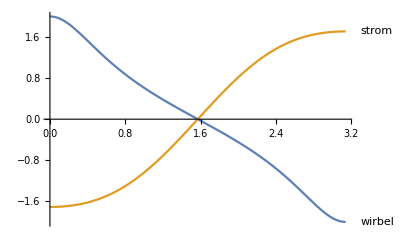

```mathematica
SetOptions[Simplify,Trig->True]
αs//FullSimplify
rotα=rotα//FullSimplify
ϕ=ϕ//FullSimplify
wirbel=(rotα/.{c->1,b->2})//Simplify
strom=(ϕ/.{c->1,b->2})//Simplify
Plot[{wirbel,strom},{u,0,π},PlotLabels->"Expressions"]
```

```mathematica
D[X,v]
```

{-Sin[u] Sin[v],Cos[v] Sin[u],0}

```mathematica
Limit[rotα,b->Infinity]
```

0